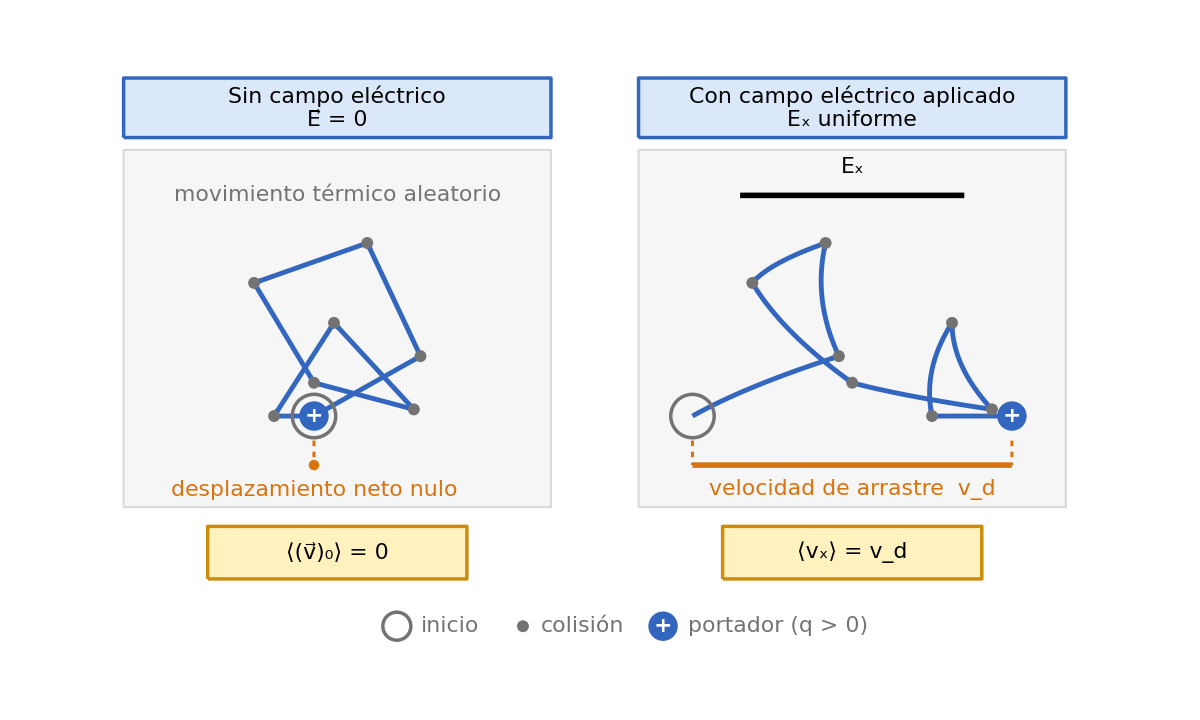

```mathematica
diagramaArrastre = Module[
  {fs, cAzul, cAzulB, cNar, cGris, cOro, cOroB, sc, oy, pc1, pc2, ox1, ox2,
   vel, a1, a2, puntos, vuelos, ext, m, ins, insI, flecha, caja, portador,
   inicio, camino, fondoPanel, hdr1, hdr2, res1, res2, fin2, xf, xm, x0, yl},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;   (* tamaño de fuente único para todo el gráfico *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cNar  = RGBColor[0.85, 0.45, 0.05];  cGris  = GrayLevel[0.45];
  cOro  = RGBColor[1.0, 0.95, 0.75];   cOroB  = RGBColor[0.80, 0.55, 0.05];

  (* ---------- Movimiento térmico: 8 recorridos libres (velocidades que suman 0) ---------- *)
  vel = {{1.6, 0.9}, {-0.8, 1.7}, {-1.7, -0.6}, {0.9, -1.5},
         {1.5, -0.4}, {-1.2, 1.3}, {-0.9, -1.4}, {0.6, 0.0}};
  a1 = {0., 0.};     (* sin campo: sin aceleración *)
  a2 = {1.2, 0.};    (* con campo: aceleración constante a lo largo de x (esquemática) *)

  puntos[a_] := FoldList[#1 + #2 + a/2 &, {0., 0.}, vel];   (* puntos de colisión *)
  vuelos[a_] := MapThread[
    Function[{p, v}, Table[p + v s + (a/2) s^2, {s, 0., 1., 0.05}]],
    {Most[puntos[a]], vel}];                                (* tramo entre colisiones *)
  ext[a_] := Module[{xs = Flatten[vuelos[a], 1][[All, 1]]}, (Min[xs] + Max[xs])/2];

  (* ---------- Geometría ---------- *)
  sc = 1.9;  oy = 3.4;               (* escala y altura de las trayectorias *)
  {pc1, pc2} = {6.5, 21.2};          (* centros de los dos paneles *)
  ox1 = pc1 - sc*ext[a1];            (* origen horizontal de cada trayectoria, centrada en su panel *)
  ox2 = pc2 - sc*ext[a2];
  fin2 = Last[puntos[a2]];
  xf = ox2 + sc*fin2[[1]];           (* posición final con campo *)
  xm = (ox2 + xf)/2;
  m[ox_, p_] := {ox + sc*p[[1]], oy + sc*p[[2]]};

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  flecha[p1_, p2_, col_] :=
    {col, AbsoluteThickness[4], Arrowheads[0.025], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  fondoPanel[pc_] :=
    {GrayLevel[0.965], EdgeForm[{AbsoluteThickness[1.5], GrayLevel[0.85]}],
     Rectangle[{pc - 6.1, 0.8}, {pc + 6.1, 11.0}, RoundingRadius -> 0.3]};
  portador[pos_] :=
    {cAzulB, Disk[pos, 0.42], Text[Style["+", fs, Bold, White], pos]};
  inicio[pos_, r_: 0.62] := {cGris, AbsoluteThickness[2.5], Circle[pos, r]};

  camino[ox_, a_] := {
    {cAzulB, AbsoluteThickness[3.5], Arrowheads[{{0.022, 0.55}}],
     Map[Function[v, Arrow[Map[Function[q, m[ox, q]], v]]], vuelos[a]]},
    {cGris, Map[Function[q, Disk[m[ox, q], 0.17]], puntos[a][[2 ;; -2]]]},
    inicio[m[ox, {0., 0.}]],
    portador[m[ox, Last[puntos[a]]]]
   };

  (* ---------- Textos ---------- *)
  hdr1 = Column[{"Sin campo eléctrico", Row[{OverVector["E"], " = 0"}]}, Center];
  hdr2 = Column[{"Con campo eléctrico aplicado",
     Row[{Subscript["E", "x"], " uniforme"}]}, Center];
  res1 = Row[{"⟨", Subscript[OverVector["v"], 0],
     "⟩ = 0"}];
  res2 = Row[{"⟨", Subscript["v", "x"],
     "⟩ = ", Subscript["v", "d"]}];

  (* ---------- Diagrama ---------- *)
  x0 = 8.2;  yl = -2.6;   (* posición de la leyenda *)
  Graphics[{
    (* paneles y cabeceras *)
    fondoPanel[pc1], fondoPanel[pc2],
    caja[{pc1, 12.2}, {12.2, 1.7}, cAzul, cAzulB], ins[hdr1, {pc1, 12.2}],
    caja[{pc2, 12.2}, {12.2, 1.7}, cAzul, cAzulB], ins[hdr2, {pc2, 12.2}],

    (* trayectorias: el mismo movimiento térmico en ambos casos *)
    camino[ox1, a1], camino[ox2, a2],

    (* panel izquierdo: sin desplazamiento neto *)
    ins["movimiento térmico aleatorio", {pc1, 9.7}, cGris],
    {cNar, AbsoluteThickness[2.2], AbsoluteDashing[{4, 4}],
     Line[{{ox1, oy - 0.7}, {ox1, 2.0}}]},
    {cNar, Disk[{ox1, 2.0}, 0.15]},
    ins["desplazamiento neto nulo", {ox1, 1.3}, cNar],

    (* panel derecho: campo aplicado y desplazamiento neto *)
    flecha[{pc2 - 3.2, 9.7}, {pc2 + 3.2, 9.7}, Black],
    ins[Row[{Subscript["E", "x"]}], {pc2, 10.5}],
    {cNar, AbsoluteThickness[2.2], AbsoluteDashing[{4, 4}],
     Line[{{ox2, oy - 0.7}, {ox2, 2.0}}], Line[{{xf, oy - 0.7}, {xf, 2.0}}]},
    flecha[{ox2, 2.0}, {xf, 2.0}, cNar],
    ins[Row[{"velocidad de arrastre  ", Subscript["v", "d"]}], {xm, 1.3}, cNar],

    (* resultados *)
    caja[{pc1, -0.5}, {7.4, 1.5}, cOro, cOroB], ins[res1, {pc1, -0.5}],
    caja[{pc2, -0.5}, {7.4, 1.5}, cOro, cOroB], ins[res2, {pc2, -0.5}],

    (* leyenda *)
    inicio[{x0, yl}, 0.4], insI["inicio", {x0 + 0.7, yl}, cGris],
    {cGris, Disk[{x0 + 3.6, yl}, 0.17]}, insI["colisión", {x0 + 4.1, yl}, cGris],
    portador[{x0 + 7.6, yl}],
    insI[Row[{"portador (", Style["q", Italic], " > 0)"}], {x0 + 8.3, yl}, cGris]
   },
   ImageSize -> 1200,
   PlotRange -> {{0, 28}, {-3.4, 13.4}},
   PlotRangePadding -> None,
   AspectRatio -> 16.8/28,
   Background -> White]
];
diagramaArrastre
```